```mathematica
mx=Simplify[1/(1/m0+σ/mstar)]
my=Simplify[1/(1/m0-σ/mstar)]
Series[mx,{m0,0,2}]
```

(m0 mstar)/(mstar+m0 σ)

(m0 mstar)/(mstar-m0 σ)

m0-(σ m0^2)/mstar+O[m0]^3

```mathematica
Series[1/mx,{m0,0,2}]
```

1/m0+σ/mstar+O[m0]^3

```mathematica
Series[a/(1+x),{x,0,2}]
```

a-a x+a x^2+O[x]^3

```mathematica
mDOSsquared=Assuming[σ^2==1,mx my//Simplify]
mDOS=Assuming[σ^2==1,√(mx my)//Simplify]
epsilon=kx^2(1/(2mx))+ky^2(1/(2my))//FullSimplify
```

(m0^2 mstar^2)/(-m0^2+mstar^2)

√(-(m0^2 mstar^2)/(m0^2-mstar^2))

(ky^2 (mstar-m0 σ)+kx^2 (mstar+m0 σ))/(2 m0 mstar)

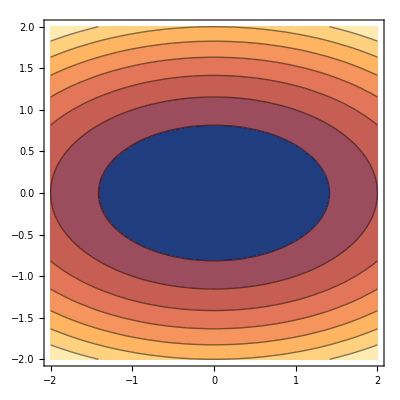

```mathematica
ContourPlot[epsilon/.{m0->1,mstar->2,σ->-1},{kx,-2,2},{ky,-2,2}]
```

```mathematica
qprimesquared=Assuming[m0>0&&mstar>0,qx^2 mDOS/mx+qy^2 mDOS/my//Simplify]
FullSimplify[(qprimesquared/.σ->1)+(qprimesquared/.σ->-1)]
```

√(1/(-m0^2+mstar^2)) (mstar (qx^2+qy^2)+m0 (qx^2-qy^2) σ)

2 mstar √(1/(-m0^2+mstar^2)) (qx^2+qy^2)

```mathematica
(m0^2 mstar^2)/(mstar^2-m0^2)//Simplify
```

(m0^2 mstar^2)/(-m0^2+mstar^2)

```mathematica
mat=({{-ⅈ w, 0, ⅈ q n0, 0, 0, 0}, {0, -ⅈ w, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ), ⅈ n0/(2ϵ), -ⅈ w, 0, ⅈ q, 0}, {ⅈ n0/(2ϵ), ⅈ n0/(2ϵ), 0, -ⅈ w, 0, ⅈ q}, {0, 0, ⅈ q (P0+e0), 0, -ⅈ w, 0}, {0, 0, 0, ⅈ q (P0+e0), 0, -ⅈ w}});
Eigensystem[-ⅈ({{0, 0, ⅈ q n0, 0, 0, 0}, {0, 0, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ m0), ⅈ n0/(2ϵ m0), 0, 0, ⅈ q/m0, 0}, {ⅈ n0/(2ϵ m0), ⅈ n0/(2ϵ m0), 0, 0c, 0, ⅈ q/m0}, {0, 0, ⅈ q (Pup+e0), 0, 0, 0}, {0, 0, 0, ⅈ q (Pdown+e0), 0, 0}})]
Eigensystem[-ⅈ({{0, 0, ⅈ q n0, 0, 0, 0}, {0, 0, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ mup), ⅈ n0/(2ϵ mup), 0, 0, ⅈ q/mup, 0}, {ⅈ n0/(2ϵ mdown), ⅈ n0/(2ϵ mdown), 0, 0, 0, ⅈ q/mdown}, {0, 0, ⅈ q (Pup+e0), 0, 0, 0}, {0, 0, 0, ⅈ q (Pdown+e0), 0, 0}})]
```

{{0,0,-1/(√2 m0 ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),1/(√2 m0 ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),-1/(√2 m0 ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),1/(√2 m0 ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))},{{-(2 q ϵ)/n0,0,0,0,1,1},{-1,1,0,0,0,0},{-(m0 Pdown q^2 ϵ^2-m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))/(m0 n0 (e0+Pdown) q ϵ),n0/(e0+Pdown),(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))) (m0 Pdown q^2 ϵ^2-m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))/(√2 m0^2 n0^2 (e0+Pdown) q^2 ϵ^2),-1/(√2 m0 (e0+Pdown) q ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),-((-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pup q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0^2 m0^2 q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pdown q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 m0^2 Pdown Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))+8 e0 m0 q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2+8 m0 Pup q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2)/(-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pdown q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))),1},{-(m0 Pdown q^2 ϵ^2-m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))/(m0 n0 (e0+Pdown) q ϵ),n0/(e0+Pdown),-((√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))) (m0 Pdown q^2 ϵ^2-m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))/(√2 m0^2 n0^2 (e0+Pdown) q^2 ϵ^2)),1/(√2 m0 (e0+Pdown) q ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),-((-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pup q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0^2 m0^2 q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pdown q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 m0^2 Pdown Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))+8 e0 m0 q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2+8 m0 Pup q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2)/(-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pdown q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))),1},{-(m0 Pdown q^2 ϵ^2-m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))/(m0 n0 (e0+Pdown) q ϵ),n0/(e0+Pdown),-(((-m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))) √(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))/(√2 m0^2 n0^2 (e0+Pdown) q^2 ϵ^2)),-1/(√2 m0 (e0+Pdown) q ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),-((-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pup q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0^2 m0^2 q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pdown q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 m0^2 Pdown Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))+8 e0 m0 q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2+8 m0 Pup q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2)/(-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pdown q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))),1},{-(m0 Pdown q^2 ϵ^2-m0 Pup q^2 ϵ^2-√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))/(m0 n0 (e0+Pdown) q ϵ),n0/(e0+Pdown),((-m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))) √(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))/(√2 m0^2 n0^2 (e0+Pdown) q^2 ϵ^2),1/(√2 m0 (e0+Pdown) q ϵ)(√(m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))),-((-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pup q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0^2 m0^2 q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pdown q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 e0 m0^2 Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-16 m0^2 Pdown Pup q^3 ϵ^3 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))+8 e0 m0 q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2+8 m0 Pup q ϵ (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))^2)/(-8 e0 m0^2 n0^2 q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2)))-8 m0^2 n0^2 Pdown q^2 ϵ^2 (m0 n0^2 q ϵ+2 e0 m0 q^2 ϵ^2+m0 Pdown q^2 ϵ^2+m0 Pup q^2 ϵ^2+√(m0^2 q^2 ϵ^2 (n0^4+Pdown^2 q^2 ϵ^2-2 Pdown Pup q^2 ϵ^2+Pup^2 q^2 ϵ^2))))),1}}}

```mathematica
Eigenvalues[-ⅈ({{0, 0, ⅈ q n0, 0, 0, 0}, {0, 0, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ mup), ⅈ n0/(2ϵ mup), 0, 0, ⅈ q/mup, 0}, {ⅈ n0/(2ϵ mdown), ⅈ n0/(2ϵ mdown), 0, 0c, 0, ⅈ q/mdown}, {0, 0, ⅈ q (Pup+e0), 0, 0, 0}, {0, 0, 0, ⅈ q (Pdown+e0), 0, 0}})]
```

{0,0,-1/(2 mdown mup ϵ)(√(mdown^2 mup n0^2 q ϵ+mdown mup^2 n0^2 q ϵ+2 e0 mdown^2 mup q^2 ϵ^2+2 e0 mdown mup^2 q^2 ϵ^2+2 mdown mup^2 Pdown q^2 ϵ^2+2 mdown^2 mup Pup q^2 ϵ^2-1/2 √((-2 mdown^2 mup n0^2 q ϵ-2 mdown mup^2 n0^2 q ϵ-4 e0 mdown^2 mup q^2 ϵ^2-4 e0 mdown mup^2 q^2 ϵ^2-4 mdown mup^2 Pdown q^2 ϵ^2-4 mdown^2 mup Pup q^2 ϵ^2)^2-4 (16 e0 mdown^3 mup^3 n0^2 q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pdown q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pup q^3 ϵ^3+16 e0^2 mdown^3 mup^3 q^4 ϵ^4+16 e0 mdown^3 mup^3 Pdown q^4 ϵ^4+16 e0 mdown^3 mup^3 Pup q^4 ϵ^4+16 mdown^3 mup^3 Pdown Pup q^4 ϵ^4)))),1/(2 mdown mup ϵ)(√(mdown^2 mup n0^2 q ϵ+mdown mup^2 n0^2 q ϵ+2 e0 mdown^2 mup q^2 ϵ^2+2 e0 mdown mup^2 q^2 ϵ^2+2 mdown mup^2 Pdown q^2 ϵ^2+2 mdown^2 mup Pup q^2 ϵ^2-1/2 √((-2 mdown^2 mup n0^2 q ϵ-2 mdown mup^2 n0^2 q ϵ-4 e0 mdown^2 mup q^2 ϵ^2-4 e0 mdown mup^2 q^2 ϵ^2-4 mdown mup^2 Pdown q^2 ϵ^2-4 mdown^2 mup Pup q^2 ϵ^2)^2-4 (16 e0 mdown^3 mup^3 n0^2 q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pdown q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pup q^3 ϵ^3+16 e0^2 mdown^3 mup^3 q^4 ϵ^4+16 e0 mdown^3 mup^3 Pdown q^4 ϵ^4+16 e0 mdown^3 mup^3 Pup q^4 ϵ^4+16 mdown^3 mup^3 Pdown Pup q^4 ϵ^4)))),-1/(2 mdown mup ϵ)(√(mdown^2 mup n0^2 q ϵ+mdown mup^2 n0^2 q ϵ+2 e0 mdown^2 mup q^2 ϵ^2+2 e0 mdown mup^2 q^2 ϵ^2+2 mdown mup^2 Pdown q^2 ϵ^2+2 mdown^2 mup Pup q^2 ϵ^2+1/2 √((-2 mdown^2 mup n0^2 q ϵ-2 mdown mup^2 n0^2 q ϵ-4 e0 mdown^2 mup q^2 ϵ^2-4 e0 mdown mup^2 q^2 ϵ^2-4 mdown mup^2 Pdown q^2 ϵ^2-4 mdown^2 mup Pup q^2 ϵ^2)^2-4 (16 e0 mdown^3 mup^3 n0^2 q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pdown q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pup q^3 ϵ^3+16 e0^2 mdown^3 mup^3 q^4 ϵ^4+16 e0 mdown^3 mup^3 Pdown q^4 ϵ^4+16 e0 mdown^3 mup^3 Pup q^4 ϵ^4+16 mdown^3 mup^3 Pdown Pup q^4 ϵ^4)))),1/(2 mdown mup ϵ)(√(mdown^2 mup n0^2 q ϵ+mdown mup^2 n0^2 q ϵ+2 e0 mdown^2 mup q^2 ϵ^2+2 e0 mdown mup^2 q^2 ϵ^2+2 mdown mup^2 Pdown q^2 ϵ^2+2 mdown^2 mup Pup q^2 ϵ^2+1/2 √((-2 mdown^2 mup n0^2 q ϵ-2 mdown mup^2 n0^2 q ϵ-4 e0 mdown^2 mup q^2 ϵ^2-4 e0 mdown mup^2 q^2 ϵ^2-4 mdown mup^2 Pdown q^2 ϵ^2-4 mdown^2 mup Pup q^2 ϵ^2)^2-4 (16 e0 mdown^3 mup^3 n0^2 q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pdown q^3 ϵ^3+8 mdown^3 mup^3 n0^2 Pup q^3 ϵ^3+16 e0^2 mdown^3 mup^3 q^4 ϵ^4+16 e0 mdown^3 mup^3 Pdown q^4 ϵ^4+16 e0 mdown^3 mup^3 Pup q^4 ϵ^4+16 mdown^3 mup^3 Pdown Pup q^4 ϵ^4))))}

```mathematica
EE=Eigenvalues[-ⅈ({{0, 0, ⅈ q n0, 0, 0, 0}, {0, 0, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ m0)+ⅈ n0/(2ϵ mstar), ⅈ n0/(2ϵ m0)+ⅈ n0/(2ϵ mstar), 0, 0, ⅈ q/m0, 0}, {ⅈ n0/(2ϵ m0)-ⅈ n0/(2ϵ mstar), ⅈ n0/(2ϵ m0)-ⅈ n0/(2ϵ mstar), 0, 0, 0, ⅈ q/m0}, {0, 0, ⅈ q (P0+e0+δP), 0, 0, 0}, {0, 0, 0, ⅈ q (P0+e0-δP), 0, 0}})]
```

{0,0,-1/(√2 m0^4 mstar^4 ϵ^4)(√(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8-√(m0^14 mstar^15 q^2 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2)))),1/(√2 m0^4 mstar^4 ϵ^4)(√(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8-√(m0^14 mstar^15 q^2 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2)))),-1/(√2 m0^4 mstar^4 ϵ^4)(√(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8+√(m0^14 mstar^15 q^2 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2)))),1/(√2 m0^4 mstar^4 ϵ^4)(√(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8+√(m0^14 mstar^15 q^2 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2))))}

```mathematica
Simplify[(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8-q m0^7 ϵ^7 √(mstar^16 n0^4+4 mstar^15 m0 n0^2 q δP ϵ+4 mstar^16 q^2 δP^2 ϵ^2))]
Simplify[(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8-q m0^7 ϵ^7  (mstar^8 n0^2))]
```

m0^7 q ϵ^7 (mstar^8 (n0^2+2 (e0+P0) q ϵ)-√(mstar^15 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2)))

2 m0^7 mstar^8 (e0+P0) q^2 ϵ^8

```mathematica
Simplify[-1/(√2 m0^4 mstar^4 ϵ^4)(√(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8-q √(m0^14 mstar^15 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2))))]
```

-1/(√2 m0^4 mstar^4 ϵ^4)(√(q (m0^7 mstar^8 ϵ^7 (n0^2+2 (e0+P0) q ϵ)-√(m0^14 mstar^15 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2)))))

```mathematica
Series[(m0^7 mstar^8 n0^2 q ϵ^7+2 e0 m0^7 mstar^8 q^2 ϵ^8+2 m0^7 mstar^8 P0 q^2 ϵ^8-√(m0^14 mstar^15 q^2 ϵ^14 (mstar n0^4+4 m0 n0^2 q δP ϵ+4 mstar q^2 δP^2 ϵ^2))),{q,0,1}]
```

$Aborted

```mathematica
Eigenvalues[-ⅈ({{0, 0, ⅈ q n0, 0, 0, 0}, {0, 0, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ m0)+ⅈ n0/(2ϵ mstar), ⅈ n0/(2ϵ m0)+ⅈ n0/(2ϵ mstar), 0, 0, ⅈ q/m0, 0}, {ⅈ n0/(2ϵ m0)-ⅈ n0/(2ϵ mstar), ⅈ n0/(2ϵ m0)-ⅈ n0/(2ϵ mstar), 0, 0, 0, ⅈ q/m0}, {0, 0, ⅈ q (P0+e0+δP), 0, 0, 0}, {0, 0, 0, ⅈ q (P0+e0-δP), 0, 0}})]
```

```mathematica
Eigenvalues[-ⅈ({{0, 0, ⅈ q/m0, 0}, {0, 0, 0, ⅈ q/m0}, {ⅈ q (P0+e0+δP), 0, 0, 0}, {0, ⅈ q (P0+e0-δP), 0, 0}})]
```

{-(q √(e0+P0-δP))/(√m0),(q √(e0+P0-δP))/(√m0),-(q √(e0+P0+δP))/(√m0),(q √(e0+P0+δP))/(√m0)}

```mathematica
EE=Eigenvalues[-ⅈ({{0, 0, ⅈ q n0, 0, 0, 0}, {0, 0, 0, ⅈ q n0, 0, 0}, {ⅈ n0/(2ϵ m0), ⅈ n0/(2ϵ m0), 0, 0, ⅈ q/m0, 0}, {ⅈ n0/(2ϵ m0), ⅈ n0/(2ϵ m0), 0, 0, 0, ⅈ q/m0}, {0, 0, ⅈ q (P0), 0, 0, 0}, {0, 0, 0, ⅈ q (P0), 0, 0}})]
```

{0,0,-(√P0 q)/(√m0),(√P0 q)/(√m0),-(√q √(n0^2+P0 q ϵ))/(√m0 √ϵ),(√q √(n0^2+P0 q ϵ))/(√m0 √ϵ)}

```mathematica
EE=Eigenvalues[-ⅈ({{0, 0, ⅈ q n0, 0, -0, 0}, {0, 0, 0, ⅈ q n0, 0, -0}, {ⅈ n0/(ϵ m0), 0, 0, 0, ⅈ q/m0, 0}, {0, 0, 0, -η, 0, ⅈ q/m0}, {0, 0, ⅈ q P0, 0, 0, 0}, {0, 0, 0, ⅈ q P0, 0, 0}})]
```

{0,0,-(√q √(n0^2+P0 q ϵ))/(√m0 √ϵ),(√q √(n0^2+P0 q ϵ))/(√m0 √ϵ),(ⅈ m0 ϵ η-√(4 m0 P0 q^2 ϵ^2-m0^2 ϵ^2 η^2))/(2 m0 ϵ),(ⅈ m0 ϵ η+√(4 m0 P0 q^2 ϵ^2-m0^2 ϵ^2 η^2))/(2 m0 ϵ)}